```mathematica
Subscript[k, 0]=20;
Subscript[X, 0]=-5;
Subscript[X, d]=-3;
δ=0.5;
Subscript[δ, 1]=0.005;

n=10;
Ti=-0.02;
Tf=0.22;
dt=(Tf-Ti)/(n-1);

tm[0]=Ti-dt;
tm[1]=Ti;
tm[n+1]=Tf+dt;

Do[tm[i]=tm[i-1]+dt,{i,2,n}]

ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

a[1]=Abs[ψ[0,Subscript[X, d],tm[1]]]*Sqrt[Subscript[δ, 1]];
b[1]=√(1-(a[1])^2);
Do[α[0,j]=ψ[0,Subscript[X, d],tm[j]],{j,1,n+1}]

Do[Do[β[i,j]=K[Subscript[X, d],0,Subscript[X, d],tm[j]-tm[i]],{j,i+1,n+1}],{i,1,n}]

Do[Do[α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}]
```

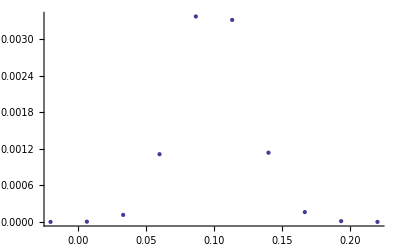

0.100506

```mathematica
ListPlot[Table[{tm[i],(a[i])^2},{i,n}],PlotRange->All]
top=(∑_(j=1)^n tm[j]*(Abs[α[0,j]])^2*Subscript[δ, 1])/(∑_(j=1)^n (Abs[α[0,j]])^2*Subscript[δ, 1])
```

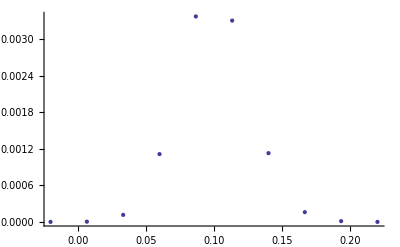

0.100381

```mathematica
Do[prob[i_]:=(∏_(k=1)^(i-1) b[k]^2)*(a[i])^2,{i,2,n,1}]
prob[1]=(a[1])^2;

ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All]

tbar=(∑_(j=1)^n (tm[j]*prob[j]))/(∑_(j=1)^n prob[j])
```

```mathematica
.1-tbar
```

-0.00038051

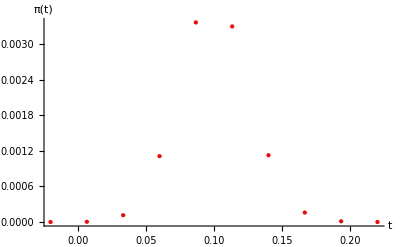

```mathematica
ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{Style["t",Italic,20],Style["π(t)",Italic,20]},Background->White,LabelStyle->Directive[Bold],TicksStyle->Directive[Black,Thick,16]]
```

Comment Section here

```mathematica
Do[ψ[i_,x_,t_]:=ψ[i-1,x,t]/b[i]-K[x,0,Subscript[X, d],t-tm[i]]*ψ[i-1,Subscript[X, d],tm[i]]*Subscript[δ, 1]/b[i],
{i,1,n}]
```

```mathematica
(* If you put in a time t this function gives you the corresponding interger that can be used to determine which Psi *)
yn[t_]:=IntegerPart[((t-Ti)+dt)/dt]
```

0.21

9

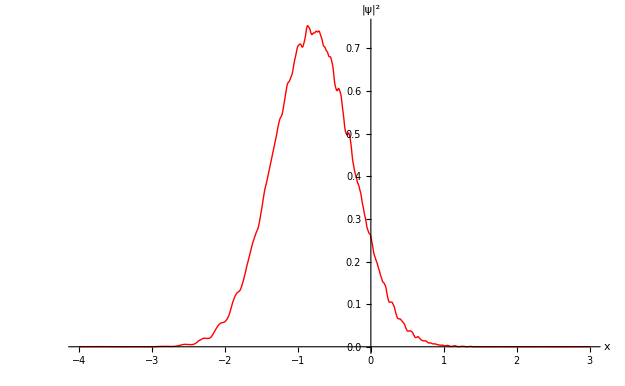

```mathematica
tplot=0.21
wn=yn[tplot]
Subscript[Prob, p][x_,t_]:=(Abs[ψ[wn,x,t]])^2

(* Subscript[Prob, p][x_,t_]:=Re[ψ[0,x,t]] *)

Plot[Subscript[Prob, p][x,tplot],{x,-4,3.0},PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{Style["x",Italic,20],Style["|ψ|^2",Italic,20]},Background->White,LabelStyle->Directive[Bold],TicksStyle->Directive[Black,Thick,16]]
```

```mathematica
(*Animate[Plot[Subscript[Prob, p][x,t],{x,-9,7},PlotRange->{{-9,7},{-1,1}},PlotStyle->Thick,AxesLabel->{Style["x",Italic,20],Style["|ψ|^2",Italic,20]},Background->LightGray,LabelStyle->Directive[Bold],TicksStyle->Directive[Black,Thick,16]],{t,0,1,.0001},AnimationRunning->False]
```

```mathematica
(* Animate[Plot[Abs[ψ[IntegerPart[((t-Ti)+dt)/dt],x,t]],{x,-9,5},PlotRange->{{-9,5},{-1,1}},PlotPoints->100],{t,tm[0],tm[n+1],dt/50},AnimationRunning->False]  *)
```

```mathematica
(* Do[psi[i_,x_,t_]:=psi[0,x,t]-psi[0,xp,tm[i]],{i,1,n-1}] *)


ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

Do[ψ[i_,x_,t_]:=(ψ[i-1,x,t]-ψ[i-1,x,tm[i]]*K[x,0,x,t-tm[i]]*Subscript[δ, 1])/b[i],{i,1,n}]
Subscript[Prob, p][x_,t_]:=(Abs[ψ[15,x,t]])^2

(* Subscript[Prob, p][x_,t_]:=Re[ψ[0,x,t]]
Subscript[Prob, d][x_,t_]:=Re[ϕ[0,x,t]] *)

Plot[{Subscript[Prob, p][x,.1]},{x,-7,-2.0},PlotRange->All,PlotStyle->Thick,AxesLabel->{Style["x",Italic,20],Style["|ψ|^2",Italic,20]},Background->LightGray,LabelStyle->Directive[Bold],TicksStyle->Directive[Black,Thick,16]]
```

$Aborted

```mathematica
Animate[Plot[{Abs[ψ[IntegerPart[((t-Ti)+dt)/dt],x,t]]^2},{x,-6,1},PlotRange->{{-10,6},{-1,1}},PlotPoints->100],{t,tm[1],tm[n+1],dt/50},AnimationRunning->False]
```